```mathematica
mu0=(-2 c (1+α)+a (1+2 α) θ+α (1+2 α) Subscript[c, d]+3 (1+α) (1+2 α) Subscript[c, r])/(3 α (1+2 α) Subscript[c, r])
```

(-2 c (1+α)+a (1+2 α) θ+α (1+2 α) c_d+3 (1+α) (1+2 α) c_r)/(3 α (1+2 α) c_r)

```mathematica
mu1=((1+α) (2 α (1+α) Subscript[c, d] (-1+Subscript[τ, r])+(-2 (1+α) (c-a θ)+(c+2 c α-a (α+θ)) Subscript[τ, m]) (-1+Subscript[τ, r])+Subscript[c, r] (2 (1+α)^2 (-3+Subscript[τ, r])+Subscript[τ, m] (3+2 α (3+α)-(1+2 α) Subscript[τ, r]))))/(α Subscript[c, r] (2 (1+α)^2 (-3+Subscript[τ, r])+Subscript[τ, m] (3+2 α (3+α)-(1+2 α) Subscript[τ, r])))
```

((1+α) (2 α (1+α) c_d (-1+τ_r)+(-2 (1+α) (c-a θ)+(c+2 c α-a (α+θ)) τ_m) (-1+τ_r)+c_r (2 (1+α)^2 (-3+τ_r)+τ_m (3+2 α (3+α)-(1+2 α) τ_r))))/(α c_r (2 (1+α)^2 (-3+τ_r)+τ_m (3+2 α (3+α)-(1+2 α) τ_r)))

```mathematica
delatmu=mu1-mu0
```

-(-2 c (1+α)+a (1+2 α) θ+α (1+2 α) c_d+3 (1+α) (1+2 α) c_r)/(3 α (1+2 α) c_r)+((1+α) (2 α (1+α) c_d (-1+τ_r)+(-2 (1+α) (c-a θ)+(c+2 c α-a (α+θ)) τ_m) (-1+τ_r)+c_r (2 (1+α)^2 (-3+τ_r)+τ_m (3+2 α (3+α)-(1+2 α) τ_r))))/(α c_r (2 (1+α)^2 (-3+τ_r)+τ_m (3+2 α (3+α)-(1+2 α) τ_r)))

```mathematica
delatmu=Simplify[delatmu]
```

1/(3 α c_r)(-(-2 c (1+α)+a (1+2 α) θ+α (1+2 α) c_d+3 (1+α) (1+2 α) c_r)/(1+2 α)+(3 (1+α) (2 α (1+α) c_d (-1+τ_r)+(-2 (1+α) (c-a θ)+(c+2 c α-a (α+θ)) τ_m) (-1+τ_r)+c_r (2 (1+α)^2 (-3+τ_r)+τ_m (3+2 α (3+α)-(1+2 α) τ_r))))/(2 (1+α)^2 (-3+τ_r)+τ_m (3+2 α (3+α)-(1+2 α) τ_r)))

```mathematica
(2 (1+α)^2 (-3 c+(-c-4 c α+2 a θ+4 a α θ+2 α (1+2 α) Subscript[c, d]) Subscript[τ, r])+Subscript[τ, m] (3 c+3 a α+3 c α+9 a α^2-8 c α^2+6 a α^3-8 c α^3-3 a α θ-8 a α^2 θ-4 a α^3 θ+(1+2 α) (c (1+7 α+6 α^2)-a (3 α^2+2 θ+α (3+θ))) Subscript[τ, r]-α (1+2 α) Subscript[c, d] (3+6 α+2 α^2-(1+2 α) Subscript[τ, r])))/(3 α (1+2 α) Subscript[c, r] (2 (1+α)^2 (-3+Subscript[τ, r])+Subscript[τ, m] (3+6 α+2 α^2-(1+2 α) Subscript[τ, r])))
```

```mathematica
a=20
c=2  
Subscript[c, r]=1
Subscript[c, d] =0.5  
θ=0.6  
α=0.4
```

20

2

1

0.5

0.6

0.4

```mathematica
result1=(2 (1+α)^2 (-3 c+(-c-4 c α+2 a θ+4 a α θ+2 α (1+2 α) Subscript[c, d]) Subscript[τ, r])+Subscript[τ, m] (3 c+3 a α+3 c α+9 a α^2-8 c α^2+6 a α^3-8 c α^3-3 a α θ-8 a α^2 θ-4 a α^3 θ+(1+2 α) (c (1+7 α+6 α^2)-a (3 α^2+2 θ+α (3+θ))) Subscript[τ, r]-α (1+2 α) Subscript[c, d] (3+6 α+2 α^2-(1+2 α) Subscript[τ, r])))/(3 α (1+2 α) Subscript[c, r] (2 (1+α)^2 (-3+Subscript[τ, r])+Subscript[τ, m] (3+6 α+2 α^2-(1+2 α) Subscript[τ, r])))
```

(0.462963 (0.78 (32.464-0.36 (5.72-1.8 τ_r)-95.184 τ_r)+3.92 (-6+38.72 τ_r)))/(0.78 (5.72-1.8 τ_r)+3.92 (-3+τ_r))

```mathematica
pic1=Plot[{result1,Subscript[τ, m]=0.78},{Subscript[τ, r],0,1},AxesLabel->{Subscript[τ, r],Δμ},PlotLegends->Placed[LineLegend[Style[TraditionalForm[#],18]&/@{"承担程度为0.78","τ_m"},LegendLayout->{"Row",2}],{0.75,0.2}]]
```

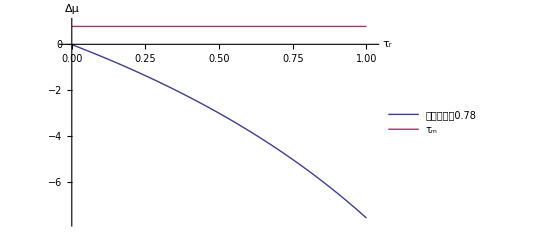

```mathematica
pic2=Plot[{result1,Subscript[τ, m]=0.5},{Subscript[τ, r],0,0.25},AxesLabel->{Subscript[τ, r],Δμ},PlotLegends->Placed[LineLegend[Style[TraditionalForm[#],18]&/@{"承担程度为0.5"},LegendLayout->{"Row",1}],{0.75,0.2}]]
```

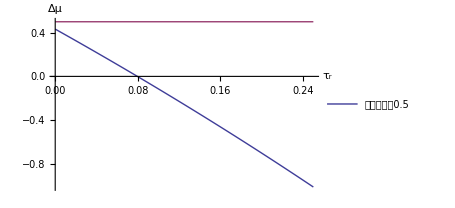

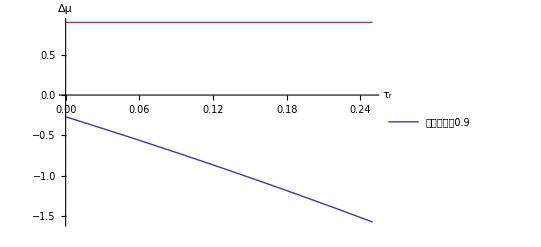

```mathematica
pic3=Plot[{result1,Subscript[τ, m]=0.9},{Subscript[τ, r],0,0.25},AxesLabel->{Subscript[τ, r],Δμ},PlotLegends->Placed[LineLegend[Style[TraditionalForm[#],18]&/@{"承担程度为0.9"},LegendLayout->{"Row",1}],{0.75,0.2}]]
```

```mathematica
Show[pic1,pic2,pic3]
```

Show[pic1,pic2,pic3]

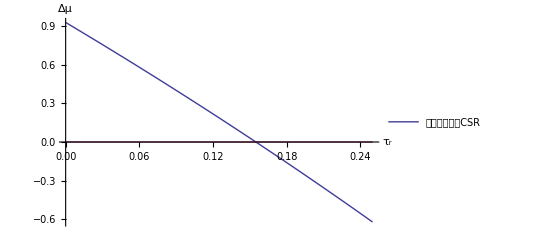

```mathematica
pic4=Plot[{result1,Subscript[τ, m]=0},{Subscript[τ, r],0,0.25},AxesLabel->{Subscript[τ, r],Δμ},PlotLegends->Placed[LineLegend[Style[TraditionalForm[#],18]&/@{"制造商不承担CSR"},LegendLayout->{"Row",1}],{0.75,0.2}]]
```

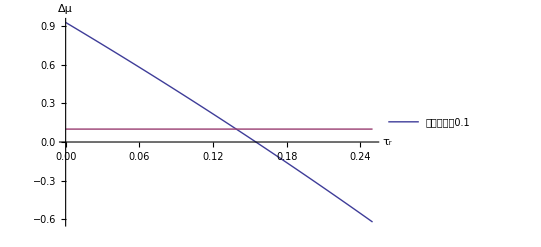

(0.462963 (0.1 (60.112-0.36 (5.72-1.8 τ_r)-207.504 τ_r)+3.92 (-6+81.92 τ_r)))/(0.1 (5.72-1.8 τ_r)+3.92 (-3+τ_r))

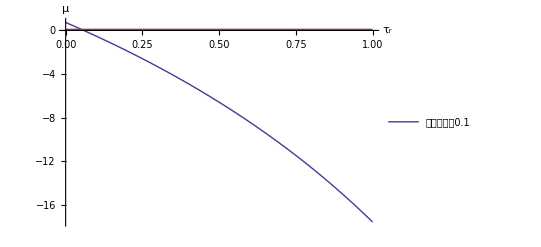

```mathematica
picr1=Plot[{result1,Subscript[τ, r]=0.1},{Subscript[τ, r],0,0.25},AxesLabel->{Subscript[τ, r],Δμ},PlotLegends->Placed[LineLegend[Style[TraditionalForm[#],18]&/@{"承担程度为0.1"},LegendLayout->{"Row",1}],{0.75,0.8}]]
```

```mathematica
delatmu
```